```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
```

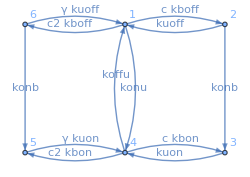

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
ClearAll[Foff1on];
offStates = {6,1,2};
onStates = {5,4,3};
Foff1on = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = Foff1on[[3]][[1]]*F31 +Foff1on[[2]][[1]]*F41 + Foff1on[[1]][[1]]*F51; (*F1off[[2]][[1]]*F41 +*)
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
rates={c>0,c2>0,γ>0,kboff>0,konb>0,kuon>0,kbon>0,koffu>0,kuoff>0,konu>0};
assum=And@@rates;
expr0 = Simplify[FoffOn];
expr1=Together[expr0]//Cancel;
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2];
exprS12PartEval = exprS12 /.{c2->10,γ->10};
exprS12PartEvalSimpl = Simplify[exprS12PartEval];

Pjoint=InverseLaplaceTransform[exprS12PartEvalSimpl,{s1,s2},{t1,t2},Assumptions->assum];(*~35s*)
```

```mathematica
exprFon = Simplify[Fon /.{c2->10,γ->10}][[1,2]][[1]];
```

```mathematica
ClearAll[τfun];
```

```mathematica
τfun[c_?NumericQ,c2_?NumericQ,γ_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ ]:=Evaluate[τ];
FoffOnfun[c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_ ]:=Evaluate[FoffOn];
```

```mathematica
ClearAll[FisherSafe]
ClearAll[FisherRate]

FisherRate[c0i_,c2i_,γi_,kboffi_,konbi_,kuoni_,kboni_,koffui_,kuoffi_,konui_ ]:=Module[{FoffOnPartEval,PjointPartEval,d2LogPjointPartEval,τPartialEval,Fjoint,Pjoint,integrand,integral},
FoffOnPartEval=FoffOnfun[c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui] ;
τPartialEval=τfun[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];

PjointPartEval=InverseLaplaceTransform[FoffOnPartEval,{s1,s2},{t1,t2}];
d2LogPjointPartEval=D[Log[PjointPartEval],{c,2}];
integrand=Evaluate[PjointPartEval* d2LogPjointPartEval/.c->c0i];

integral=-NIntegrate[integrand,{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->10];
c0i^2*integral/τPartialEval
];
```

```mathematica
δ=1/10;
ClearAll[expr1];
ClearAll[expr2];
ClearAll[exprS1];
ClearAll[exprS12];
expr1 = FoffOn /.{γ->1};
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2];
```

```mathematica
ClearAll[Pjoint];
Pjoint=InverseLaplaceTransform[exprS12,{s1,s2},{t1,t2},Assumptions->assum];
```

```mathematica
PjointSimpl=Simplify[Pjoint,{A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konu (konb+kuoff)),B==c kbon+c2 kbon+koffu+kuon,D==-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2}]
```

1/(4 √A √D)ⅇ^(-1/2 (√A+c kboff+c2 kboff+konb+konu+kuoff) t1-1/2 (B+√D) t2) koffu (√A (1+ⅇ^(√A t1)) konu (B-B ⅇ^(√D t2)+√D (1+ⅇ^(√D t2))+2 (-1+ⅇ^(√D t2)) kuon)+(-1+ⅇ^(√A t1)) (-c2 √D kboff konu-c2 √D ⅇ^(√D t2) kboff konu-c √D (1+ⅇ^(√D t2)) kboff konu+√D konb konu+√D ⅇ^(√D t2) konb konu-√D konu^2-√D ⅇ^(√D t2) konu^2+B (-1+ⅇ^(√D t2)) konu (c kboff+c2 kboff-konb+konu-kuoff)+√D konu kuoff+√D ⅇ^(√D t2) konu kuoff-4 c2 kboff konb kuon+4 c2 ⅇ^(√D t2) kboff konb kuon+2 c (-1+ⅇ^(√D t2)) kboff (2 konb-konu) kuon+2 c2 kboff konu kuon-2 c2 ⅇ^(√D t2) kboff konu kuon-2 konb konu kuon+2 ⅇ^(√D t2) konb konu kuon+2 konu^2 kuon-2 ⅇ^(√D t2) konu^2 kuon-2 konu kuoff kuon+2 ⅇ^(√D t2) konu kuoff kuon))

```mathematica
d2LogPjoint =D[Log[Pjoint],{c,2}];
integrand = Pjoint *d2LogPjoint ;(*-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2*)
```

```mathematica
integrandSimpl1=integrand//.{c kbon+c2 kbon+koffu+kuon->Bon,
-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2->D,
(-(c kboff)/2-(c2 kboff)/2-konb/2-konu/2-kuoff/2)->-Boff/2,
-(c kbon)/2-(c2 kbon)/2-koffu/2-kuon/2->-Bon/2,(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konb konu+konu kuoff)->A,(-4 kboff konb+2 kboff (c kboff+c2 kboff+konb+konu+kuoff))->E}
```

```mathematica
integrandC=Compile[{{c,_Real},{c2,_Real},{t1,_Real},{t2,_Real},{kboff,_Real},{konb,_Real},{kuon,_Real},{kbon,_Real},{koffu,_Real},{kuoff,_Real},{konu,_Real}},
Evaluate[integrand],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
integrandC[1,1,1,1,1,1,1,1,1,1,1.]
```

0.00346896

```mathematica
ClearAll[integrandCNum];
integrandCNum[c_?NumericQ,c2_?NumericQ,t1_?NumericQ,t2_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ]:=integrandC[N[c],N[c2],N[t1],N[t2],N[kboff],N[konb],N[kuon],N[kbon],N[koffu],N[kuoff],N[konu]];
```

```mathematica
integrandCNum[1,3,1,1,1,1,1,1,1,1,1]
```

0.00107171

```mathematica
kmin =0.001;
kmax = 5.;
kdl=0.0888;
c0=40.;
ω=0.;
c2=ω*c0;
γ=1;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
integral=-NIntegrate[integrandCNum[c0,c2,t1,t2,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->1}, 
PrecisionGoal->4,
AccuracyGoal->4,
MinRecursion->3,
MaxRecursion->10];
integral*c0^2/τfun[c0,c2,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
(*τfun[c_,c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_ ]*)
```

0.806061

```mathematica
ClearAll[FisherFast];
ClearAll[FisherSafe];
FisherFast[c0i_?NumericQ,c2i_?NumericQ,γi_?NumericQ,kboffi_?NumericQ,konbi_?NumericQ,kuoni_?NumericQ,kboni_?NumericQ,koffui_?NumericQ,kuoffi_?NumericQ,konui_?NumericQ ]:=Module[{τPartialEval,integral},
τPartialEval=τfun[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];
integral=-NIntegrate[integrandCNum[c0i,c2i,t1,t2,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->6];
integral*c0i^2/τPartialEval];
```

```mathematica
FisherNum[c0i_?NumericQ,c2i_?NumericQ,γi_?NumericQ,kboffi_?NumericQ,konbi_?NumericQ,kuoni_?NumericQ,kboni_?NumericQ,koffui_?NumericQ,kuoffi_?NumericQ,konui_?NumericQ ]:=NIntegrate[Module[{f0,fp,fm,dlog,PjointPartEval,τPartialEval},
τPartialEval=τfun[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];
PjointPartEval=Pjoint/.{konb->konbi,kuon->kuoni, koffu->koffui,kboff->kboffi,kbon->kboni,konu->konui,kuoff->kuoffi};
f0=PjointPartEval/. {t1->t1i,t2->t2i,c->c0i};
fp=PjointPartEval/. {t1->t1i,t2->t2i,c->c0i+δ};
fm=PjointPartEval/. {t1->t1i,t2->t2i,c->c0i-δ};
(*central-difference derivative of log-pdf*)
dlog=(Log[fp]-Log[fm])/(2 δ);
N[dlog^2*f0*c0i^2/τPartialEval,20]],{t1i,0,∞},{t2i,0,∞},
Method->{"GlobalAdaptive","SymbolicProcessing"->1}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->10,
WorkingPrecision->20];

ClearAll[FisherSafe];
FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherFast[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
],{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
];
```

```mathematica
kmin =0.001;
kmax = 5.;
kdl=0.0888;
c0=40.;
ω=0.;
c2=ω*c0;
γ=1.;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
FisherSafe[c0,c2,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.806061

```mathematica
FisherSafeLog[c0_,c2_,γ_,lnkboff,lnkonb,lnkuon,lnkbon,lnkoffu,lnkuoff,lnkonu]:=FisherSafe[c0,c2,γ,Exp[lnkboff],Exp[lnkonb],Exp[lnkuon],Exp[lnkbon],Exp[lnkoffu],Exp[lnkuoff],Exp[lnkonu]];
```

```mathematica
cvals=10^Range[-1.,2.,3/13];
```

```mathematica
ω=0.1;
γ=1.;
kmin =0.001;
kmax = 5;
kdl=0.0888;
(*c0,c2,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu*)
{res,data}=
ParallelTable[
Reap[
NMaximize[
{FisherSafe[cvals[[i]],ω*cvals[[i]],γ,kboff,kmax,kmax,kbon,kmax,kuoff,konu],
kmin<=kboff<=kdl,
kmin<=kbon<=kdl,
kmin<=kuoff<=kmax,
kmin<=konu<=kmax},
{kboff,kbon,kuoff,konu},
Method->"NelderMead",
PrecisionGoal->3,AccuracyGoal->3,MaxIterations->1,
StepMonitor:>Print["Rates = ",{kboff,kbon,kuoff,konu}],
EvaluationMonitor:>Sow[{kboff,kbon,kuoff,konu}]
]
],{i,1,14}
]
```

```mathematica
results={0.0000759879964592278,0.00022150021879408684,0.0006148773449528048,0.0016562801910414,0.004300300247753413,0.010618539124217783,0.024622807047113327,0.05281776305818426,0.10318803735623742,0.18025419461855827,0.27542787139230235,0.35986679771752145,0.3990372787774877,0.3923907460563668};
resultsWithIntermediateEvals={{{0.0000759879964592278,{kboff->0.08678292151749663,kbon->0.0888,kuoff->4.949563268516092,konu->0.5131189228920989}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08678292151749663,0.0888,4.949563268516092,0.5131189228920989},{0.08678292151749663,0.0888,4.949563268516092,0.5131189228920989}}}},{{0.00022150021879408684,{kboff->0.08858362439009515,kbon->0.0888,kuoff->4.949548023208307,konu->0.5129736615494083}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08858362439009515,0.0888,4.949548023208307,0.5129736615494083},{0.08858362439009515,0.0888,4.949548023208307,0.5129736615494083}}}},{{0.0006148773449528048,{kboff->0.0888,kbon->0.0888,kuoff->4.949545493907327,konu->0.5129538692064105}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.949545493907327,0.5129538692064105},{0.0888,0.0888,4.949545493907327,0.5129538692064105}}}},{{0.0016562801910414,{kboff->0.0888,kbon->0.0888,kuoff->4.949536590712166,konu->0.5128769548831933}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.949536590712166,0.5128769548831933},{0.0888,0.0888,4.949536590712166,0.5128769548831933}}}},{{0.004300300247753413,{kboff->0.0888,kbon->0.0888,kuoff->4.9495079825920065,konu->0.5126249250465735}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.9495079825920065,0.5126249250465735},{0.0888,0.0888,4.9495079825920065,0.5126249250465735}}}},{{0.010618539124217783,{kboff->0.0888,kbon->0.0888,kuoff->4.949495504070001,konu->0.5125359105994716}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.949495504070001,0.5125359105994716},{0.0888,0.0888,4.949495504070001,0.5125359105994716}}}},{{0.024622807047113327,{kboff->0.0888,kbon->0.0888,kuoff->4.949392300628133,konu->0.5116757951510611}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.949392300628133,0.5116757951510611},{0.0888,0.0888,4.949392300628133,0.5116757951510611}}}},{{0.05281776305818426,{kboff->0.0888,kbon->0.0888,kuoff->4.949223760620292,konu->0.5103410604172148}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.949223760620292,0.5103410604172148},{0.0888,0.0888,4.949223760620292,0.5103410604172148}}}},{{0.10318803735623742,{kboff->0.0888,kbon->0.0888,kuoff->4.94898282154941,konu->0.5084926326344213}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.94898282154941,0.5084926326344213},{0.0888,0.0888,4.94898282154941,0.5084926326344213}}}},{{0.18025419461855827,{kboff->0.0888,kbon->0.0888,kuoff->4.948737747266848,konu->0.506525553423034}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.948737747266848,0.506525553423034},{0.0888,0.0888,4.948737747266848,0.506525553423034}}}},{{0.27542787139230235,{kboff->0.0888,kbon->0.0888,kuoff->4.94860593912183,konu->0.504858765957231}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.94860593912183,0.504858765957231},{0.0888,0.0888,4.94860593912183,0.504858765957231}}}},{{0.35986679771752145,{kboff->0.0888,kbon->0.0888,kuoff->4.948754274298518,konu->0.5040303771636044}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.0888,0.0888,4.948754274298518,0.5040303771636044},{0.0888,0.0888,4.948754274298518,0.5040303771636044}}}},{{0.3990372787774877,{kboff->0.08317295345845865,kbon->0.08840272099922851,kuoff->4.949593811831308,konu->0.513415599728968}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968}}}},{{0.3923907460563668,{kboff->0.08317295345845865,kbon->0.08840272099922851,kuoff->4.949593811831308,konu->0.513415599728968}},{{{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.06520829567211424,0.07062977639816195,2.7490263991791895,4.96476291273906},{0.030814038359738637,0.021620089929918915,4.9360099852095045,0.9704380243496205},{0.058189134637888905,0.06348373855830367,3.4973711019276847,1.7499921131796818},{0.08804719011429353,0.03206067647177377,4.938789124272504,1.6422721161353118},{0.011308385075389855,0.01282889258299769,0.2863713162679901,3.2410916375368934},{0.08534855038382547,0.08106824809608146,4.983457986255287,1.4226409456649431},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968},{0.08317295345845865,0.08840272099922851,4.949593811831308,0.513415599728968}}}}};
```

```mathematica
f[i_]:=results[[i]];
```

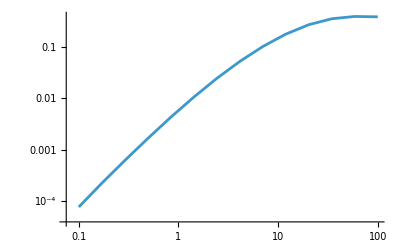

```mathematica
ListLinePlot[Table[{cvals[[i]],results[[i]]},{i,1,14}],ScalingFunctions->{"Log","Log"}]
```

```mathematica
i=14;(*c0,c2,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu*)
kdl=5*0.503427/100;
FisherSafe[cvals[[i]],0*cvals[[i]],γ,kdl,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.804384

```mathematica
(*Understanding Compile*)
expr[a_,b_,t_]:=Exp[-a*t]+Exp[-b*t];
cexpr=Compile[{{t,_Real},{a,_Real},{b,_Real}},expr[a,b,t]];
cexpr[1.,2.,1.]
```

0.503215

```mathematica
(*Parallelization*)
c2vals={0.0,0.5,1};
ParallelTable[FisherSafe[c0,c2vals[[i]],1.,0.08317295345845865,kmax,kmax,kmin,kmax,kmin,kmin],{i,1,3}]]
```

{{0.806061,0.786207,0.766968},{}}

```mathematica
(*Compilation*)
Needs["CCompilerDriver`"]

expr[a_,t_]:=a*Exp[-a*t];
CForm[expr[a,t]]
```

a/Power(E,a*t)

```mathematica
stream=OpenWrite["/home/tohme/.julia/dev/LLROpt/C/integrand.c"];
WriteString[stream,"double evalExpr(double a, double t) {\n  return ",ToString[CForm[expr[a,t]],InputForm],";\n}\n"];
Close[stream];
```

```mathematica
(*Sandbox*)
expr[a_,t_]:=a*Exp[-a*t];
exprC=Compile[{{a,_Real},{t,_Real}},Evaluate[expr[a,t]],RuntimeOptions->"Speed",CompilationTarget->"C"];
f[a_?NumericQ][t_?NumericQ]:=exprC[a,t];
NIntegrate[f[9.3687][t],{t,0,∞}]
```

1.